```mathematica
Exit
```

```mathematica
PacletDirectoryLoad["~/Documents/projects/linear_teukolsky/mod_SpinWeightedSpheroidalHarmonics2"];
```

```mathematica
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
Get["Documents/KerrSpinningFluxes/SpinningTrajectory.wl"]
Get["Documents/KerrSpinningFluxes/TeukolskySpinFluxes.wl"]
```

```mathematica
NotebookEvaluate["~/Documents/projects/linear_teukolsky/packages/LinearizedTeukolskyEquations_new.nb"]
```

```mathematica
NotebookEvaluate["~/Documents/projects/linear_teukolsky/packages/TrajectoryDerivatives.nb"]
```

```mathematica
NotebookEvaluate["~/Documents/projects/linear_teukolsky/packages/Functions_for_spherical_orbits_fixed_turning_point_on_average_new.nb"]
```

```mathematica
KerrSpinOrbitCorrectionSphericalNew[aint_,pint_,eint_?PossibleZeroQ,xint_,kmax_]:=Module[{orbitGeo,constmot,δconstmot,ξzcoeff,δΥz,Υgsph,Υrg,Υzg,Υϕg,Υtg,dtgdλcoeff,dϕgdλcoeff,dtspindλsparcoeff,dϕspindλsparcoeff,δΥt,δΥϕ},
orbitGeo=KerrGeoOrbit[aint,pint,eint,xint,"Parametrization"->"Phases","Method"->"Analytic"];
constmot={Egsph[aint,pint,xint],Jzgsph[aint,pint,xint],Jzgsphx0[aint,pint,xint],Kgsph[aint,pint,xint]}; (* Calculation constants of motion. Jzgsphx0 serves for regularize polar orbits. *)
δconstmot=δconstmotionsph[aint, pint, xint,constmot]; (* Calculation shifts to the constants of motion *)
ξzcoeff=ξzsparcoeffsph[kmax,aint,pint,xint,constmot]; (* Near identify shif functions. It is need for the shift to the theta trajactory.*)
δΥz=Re[δΥzsph[aint,pint,xint,constmot]-devsph[aint,pint,xint,constmot]]; (* Spin correction to the theta frequency in the fixed (on average) "gauge"*)

Υgsph=Values[orbitGeo["Frequencies"]];
{Υrg,Υzg,Υϕg,Υtg}=Υgsph;  (*Geodesic theta frequency*)
dtgdλcoeff=dtgdλcoeffsph[kmax,aint,pint,xint,constmot];  (*Fourier coefficients of geodesic coordinate time velocity.*)

dtspindλsparcoeff=dtspindλsparcoeffsph[kmax,aint,pint,xint,constmot,δconstmot,ξzcoeff]; (*Fourier coefficients of spin correction to the coordinate time velocity.*)
dϕgdλcoeff=dϕgdλcoeffsph[kmax,aint,pint,xint,constmot];  (*Fourier coefficients of geodesic azimuthal velocity.*)
dϕspindλsparcoeff=dϕspindλsparcoeffsph[kmax,aint,pint,xint,constmot,δconstmot,ξzcoeff];  (*Fourier coefficients of spin correction to the azimthual velocity.*)
δΥt=Re[dtspindλsparcoeff[[kmax+1]]];  (* Spin correction to the coordinate time frequency in the fixed (on average) "gauge"*)
δΥϕ=Re[dϕspindλsparcoeff[[kmax+1]]];   (* Spin correction to the azimuthal frequency in the fixed (on average) "gauge"*)
<|
"a"->aint,
"p"->pint,
"e"->eint,
"Inclination"->xint,
"En0"->constmot[[1]],
"Lz0"->constmot[[2]],
"K0"->constmot[[4]],
"TrajectoryGeo"->orbitGeo["Trajectory"],
"MinoFrequenciesGeo"->{Υtg,Υzg,Υϕg},
"BLFrequenciesGeo"->{Υzg,Υϕg}/Υtg,
"TrajectoryDeltas"->orbitGeo["TrajectoryDeltas"],
"MinoFrequenciesCorrection"->{δΥt,δΥz,δΥϕ},
"BLFrequenciesCorrection"->{δΥz/Υtg-Υzg*δΥt/Υtg^2,δΥϕ/Υtg-Υϕg*δΥt/Υtg^2},
"δEn"->δconstmot[[1]],
"δLz"->δconstmot[[2]],
"δK"->δconstmot[[3]],
"OrbitCorrection"->Function[{qz},<|
"δΔt"->Δtspinsparsph[qz,dtgdλcoeff,dtspindλsparcoeff,Υzg,δΥz],
"δr"->δrspinsparsph[qz,aint,pint,xint,constmot,δconstmot],
"δz"->zspinsparsph[qz,aint,pint,xint,constmot,δconstmot,ξzcoeff],
"δΔϕ"->Δϕspinsparsph[qz,dϕgdλcoeff,dϕspindλsparcoeff,Υzg,δΥz],
"δUr"->drdλspinsparsph[qz,aint,pint,xint,constmot],
"δUz"->dzdλspinsparsph[qz,aint,pint,xint,constmot,δconstmot,ξzcoeff]
|>]
|>
]
```

```mathematica
a=0.90000000000000002220446049250313080847263336181640625`48.
p=10.6926374295956652105132889118976891040802001953125`48.
e=0
x=0.524999999999999911182158029987476766109466552734375`48.
```

0.900000000000000022204460492503130808472633361816

10.6926374295956652105132889118976891040802001953

0

0.524999999999999911182158029987476766109466552734

```mathematica
corr=KerrSpinOrbitCorrectionSphericalNew[a,p,e,x,32]
```

<|a→0.900000000000000022204460492503130808472633361816,p→10.6926374295956652105132889118976891040802001953,e→0,Inclination→0.524999999999999911182158029987476766109466552734,En0→0.9564793156581303118496830339056623990790648147,Lz0→1.93011745844533068445928697368777597924816733,K0→10.9840003807117862134449903242074375216382984,TrajectoryGeo→{Function[{qt$,qr$,qθ$},qt$+41.4032353688208271459167442097718547965370816 (0.999079974358326009243844583941105087673694196 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.00092129745805532503251762845690741854014058 (π/2+qθ$),0.00367756283532698007494451385301947807615038274],0.00367756283532698007494451385301947807615038274])-0.340520869569868854086492306028301446001888119 (203.6680215398415490851720672574100665447136 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.])+92.660090733179242044783334613401282696024811 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.]+(0. JacobiCN[0.5 qr$,0.] JacobiSN[0.5 qr$,0.])/(√(1+0. JacobiSN[0.5 qr$,0.]^2)))),Listable],Function[{qr$},(-97.3553938993835001325128033926365974963684226+0. JacobiSN[0.5 qr$,0.]^2)/(-9.10489994076839542976638279353252174831486789+0. JacobiSN[0.5 qr$,0.]^2),Listable],Function[{qθ$},ArcCos[0.851102226527460150821248032905960103230886317803 JacobiSN[1.00092129745805532503251762845690741854014058 (π/2+qθ$),0.00367756283532698007494451385301947807615038274]],Listable],Function[{qϕ$,qr$,qθ$},qϕ$-0.523665623995535822836242025626454689503266731 (1.9070638456886595919987230321711442834719335 (π/2+qθ$)-EllipticPi[0.724375000000000093258734068513141506976007909511,JacobiAmplitude[1.00092129745805532503251762845690741854014058 (π/2+qθ$),0.00367756283532698007494451385301947807615038274],0.00367756283532698007494451385301947807615038274])+5.232391923669872009257769097448236739773259 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.]),Listable]},MinoFrequenciesGeo→{134.36127834312039429212576577092131921971518,3.682389667243266054426297889444953384062524,3.8571430285481983073018284040013998813690931},BLFrequenciesGeo→{0.027406628700268040086463286491698636479266824,0.02870725164357364034834177068564787652750378},TrajectoryDeltas→<|Δtr→Function[{qr$},-0.340520869569868854086492306028301446001888119 (203.6680215398415490851720672574100665447136 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.])+92.660090733179242044783334613401282696024811 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.]+(0. JacobiCN[0.5 qr$,0.] JacobiSN[0.5 qr$,0.])/(√(1+0. JacobiSN[0.5 qr$,0.]^2)))),Listable],Δtθ→Function[{qθ$},41.4032353688208271459167442097718547965370816 (0.999079974358326009243844583941105087673694196 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.00092129745805532503251762845690741854014058 (π/2+qθ$),0.00367756283532698007494451385301947807615038274],0.00367756283532698007494451385301947807615038274]),Listable],Δϕr→Function[{qr$},5.232391923669872009257769097448236739773259 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.]),Listable],Δϕθ→Function[{qθ$},-0.523665623995535822836242025626454689503266731 (1.9070638456886595919987230321711442834719335 (π/2+qθ$)-EllipticPi[0.724375000000000093258734068513141506976007909511,JacobiAmplitude[1.00092129745805532503251762845690741854014058 (π/2+qθ$),0.00367756283532698007494451385301947807615038274],0.00367756283532698007494451385301947807615038274]),Listable]|>,MinoFrequenciesCorrection→{-0.537326065549056431494781827562069381783,-0.0983488747958261749917363703469780321885524,-0.1769775805392063163909357847703418120442},BLFrequenciesCorrection→{-0.00062237111657124216918648221698066839172224,-0.001202373391746685948290171367577292210922},δEn→-0.0015057006909722783750170869132926324218534,δLz→0.1997286692590264517659682425336774579081826,δK→6.716840934374854055216951782163310195086761,OrbitCorrection→Function[{qz$},Association[δΔt→Δtspinsparsph[qz$,dtgdλcoeff$10471,dtspindλsparcoeff$10471,Υzg$10471,δΥz$10471],δr→δrspinsparsph[qz$,0.900000000000000022204460492503130808472633361816,10.6926374295956652105132889118976891040802001953,0.524999999999999911182158029987476766109466552734,constmot$10471,δconstmot$10471],δz→zspinsparsph[qz$,0.900000000000000022204460492503130808472633361816,10.6926374295956652105132889118976891040802001953,0.524999999999999911182158029987476766109466552734,constmot$10471,δconstmot$10471,ξzcoeff$10471],δΔϕ→Δϕspinsparsph[qz$,dϕgdλcoeff$10471,dϕspindλsparcoeff$10471,Υzg$10471,δΥz$10471],δUr→drdλspinsparsph[qz$,0.900000000000000022204460492503130808472633361816,10.6926374295956652105132889118976891040802001953,0.524999999999999911182158029987476766109466552734,constmot$10471],δUz→dzdλspinsparsph[qz$,0.900000000000000022204460492503130808472633361816,10.6926374295956652105132889118976891040802001953,0.524999999999999911182158029987476766109466552734,constmot$10471,δconstmot$10471,ξzcoeff$10471]]]|>

```mathematica
derivatives=derivativesSph[a,p,x]
```

<|Υz→3.682389667243266054426297889444953384062524,Υt→134.36127834312039429212576577092131921971518,Υϕ→3.8571430285481983073018284040013998813690931,dΥzdx→-0.2660147481753567007445381459136057834201612,dΥzdr→0.1318163765588665515552722116512192203880252,dΥtdx→-1.55154209292186939932424278336084781254945,dΥtdr→22.829031391438135830094894913453358965074477,dΥϕdx→-0.307215134586473103222965444751710319597907,dΥϕdr→0.11377781057174953378550410363616589408524,dBLFrequenciesdr→{-0.003675541171258349863189246073838153218757522,-0.00403078137570456739581195587392328384336039},dMinoFrequenciesdr→{22.829031391438135830094894913453358965074477,0.1318163765588665515552722116512192203880252,0.11377781057174953378550410363616589408524},dBLFrequenciesdx→{-0.0016633676969868868952534269591396085231289,-0.00195498754201022102395596229269414302541399},dMinoFrequenciesdx→{-1.55154209292186939932424278336084781254945,-0.2660147481753567007445381459136057834201612,-0.307215134586473103222965444751710319597907},dEndr→0.0037115719098462872007205316769994759132962749,dLzdr→0.069577690640748525595330506470765187978796812,dEndx→-0.00297423764666649270882919004995487000429569318,dLzdx→3.53373101012528345699755515489936254805484605,OrbitDerivatives→Function[{qz$},sn$17343=JacobiSN[(Kkz$17343 2 (qz$+π/2))/π,kz$17343];cn$17343=JacobiCN[(2 (qz$+π/2) Kkz$17343)/π,kz$17343];dn$17343=JacobiDN[(2 (qz$+π/2) Kkz$17343)/π,kz$17343];epsilon$17343=JacobiEpsilon[(2 (qz$+π/2) Kkz$17343)/π,kz$17343];cd$17343=JacobiCD[(2 (qz$+π/2) Kkz$17343)/π,kz$17343];sc$17343=JacobiSC[((π+2 qz$) Kkz$17343)/π,kz$17343];dsndkz$17343=-(cn$17343 dn$17343 (2 (qz$+π/2) Ekz$17343-π epsilon$17343+kz$17343 π cd$17343 sn$17343))/(2 (-1+kz$17343) kz$17343 π);dzdr$17343=z1$17343 dsndkz$17343 dkzdr$17343;dzdx$17343=z1$17343 dsndkz$17343 dkzdx$17343-(sn$17343 0.524999999999999911182158029987476766109466552734)/(√(1-0.524999999999999911182158029987476766109466552734^2));dUzdr$17343=(dQdr$17343 cn$17343 dn$17343)/(2 √Q$17343)+(√Q$17343 sn$17343 ((kz$17343 cn$17343^2+dn$17343^2) (((π+2 qz$) Ekz$17343)/π-epsilon$17343)+kz$17343 dn$17343 (cn$17343^2 sc$17343+dn$17343 cd$17343 sn$17343)) dkzdr$17343)/(2 (-1+kz$17343) kz$17343);dUzdx$17343=(dQdx$17343 cn$17343 dn$17343)/(2 √Q$17343)+(√Q$17343 sn$17343 ((kz$17343 cn$17343^2+dn$17343^2) (((π+2 qz$) Ekz$17343)/π-epsilon$17343)+kz$17343 dn$17343 (cn$17343^2 sc$17343+dn$17343 cd$17343 sn$17343)) dkzdx$17343)/(2 (-1+kz$17343) kz$17343);am$17343=JacobiAmplitude[(Kkz$17343 2 (qz$+π/2))/π,kz$17343];damdkz$17343=(dn$17343 (-2 (qz$+π/2) Ekz$17343+π epsilon$17343)-kz$17343 π cn$17343 sn$17343)/(2 (-1+kz$17343) kz$17343 π);dΔtzdr$17343=dttildedr$17343[am$17343]-(dttildedr$17343[π] (qz$+π/2))/π+((En$17343 z2$17343 dn$17343) damdkz$17343 dkzdr$17343)/(-1+En$17343^2);dΔtzdx$17343=dttildedx$17343[am$17343]-(dttildedx$17343[π] (qz$+π/2))/π+((En$17343 z2$17343 dn$17343) damdkz$17343 dkzdx$17343)/(-1+En$17343^2);dΔϕzdr$17343=-(dϕtildedr$17343[am$17343]-(dϕtildedr$17343[π] (qz$+π/2))/π+(Lz$17343 damdkz$17343 dkzdr$17343)/(dn$17343 (-z2$17343+z1$17343^2 z2$17343 sn$17343^2)));dΔϕzdx$17343=-(dϕtildedx$17343[am$17343]-(dϕtildedx$17343[π] (qz$+π/2))/π+(Lz$17343 damdkz$17343 dkzdx$17343)/(dn$17343 (-z2$17343+z1$17343^2 z2$17343 sn$17343^2)));Association[dzdr→dzdr$17343,dzdx→dzdx$17343,dUzdr→dUzdr$17343,dUzdx→dUzdx$17343,dΔtdr→dΔtzdr$17343,dΔtdx→dΔtzdx$17343,dΔϕdr→dΔϕzdr$17343,dΔϕdx→dΔϕzdx$17343]]|>

```mathematica
l=2
m=2
k=1
```

2

2

1

```mathematica
mode=TeukolskySpinModeSphericalCorrection[l,m,k,corr,derivatives,{angparNew,TeukolskySolverHS1spin},WorkingPrecision->32]
```

-1.857317458751006×10^-6

<|l→2,m→2,k→1,n→0,ω→0.08482113198741532078314682786299438953427438,ωCorrection→-0.003027117900064614065766824952135252813566,ωDerivatives→<|r→-0.0117371039226674846548131578216847209054783,x→-0.00557334278100732894316535154452789457395687|>,Amplitudes→<|ℐ→-1.85731745875100623103043853×10^-6-5.057555011239560040095533031×10^-6 ⅈ,ℋ→0.00001947195421864441581810003695-0.00006713662018773599122201117818 ⅈ|>,AmplitudesCorrection→<|ℐ→-9.0356817029286524494057473×10^-8-3.4844944705006888707110101×10^-7 ⅈ,ℋ→-9.51408107621423635543194812×10^-6+0.00003200755412817525239048888157 ⅈ|>,AmplitudesDerivatives→<|r→<|ℐ→1.10271214638607127578635571×10^-6+2.64391812756748529070830818×10^-6 ⅈ,ℋ→-8.48163368732796425256805854×10^-6+0.00002530969618877660322358736589 ⅈ|>,x→<|ℐ→-9.6376366681388092907220754×10^-7-2.79719240331379945939155718×10^-6 ⅈ,ℋ→8.78101122184822395133293605×10^-6-0.0000320895210981242246594537091 ⅈ|>|>,α→-0.0042977388708526388209407267145965638681,dαdω→-0.12748889349022469370435564621626274696,S→0.152354,Fluxes→<|Energy→<|ℐ→3.2107498109748156184427077×10^-10,ℋ→-2.32283522897401781242936425×10^-10|>,AngularMomentum→<|ℐ→7.57063655187055457077861056×10^-9,ℋ→-5.477020111730295036103172176×10^-9|>|>,FluxesCorrection→<|Energy→<|ℐ→6.561418481261008012327674×10^-11,ℋ→2.261895119146000635650791777×10^-10|>,AngularMomentum→<|ℐ→1.8173016020246124725203695×10^-9,ℋ→5.137863973268192512212529972×10^-9|>|>,FluxesDerivatives→<|r→<|Energy→<|ℐ→-2.52250799902143758958866979×10^-10,ℋ→1.93838484609388615147367394×10^-10|>,AngularMomentum→<|ℐ→-4.9002441030367973846916663×10^-9,ℋ→3.81264205515247965064137403×10^-9|>|>,x→<|Energy→<|ℐ→3.94741339248199202669321303×10^-10,ℋ→-2.13199028948065993184155624×10^-10|>,AngularMomentum→<|ℐ→9.80506168196140006049571892×10^-9,ℋ→-5.38690486310732625060702335×10^-9|>|>|>,λ→3.49258887047343078523145896892937596943,dλdω→-5.96456782127994662293063002661399673,stepsθ→64|>

```mathematica
1-mode["AmplitudesCorrection"]["ℐ"]/(-9.03568171073413*^-8+(-3.484494547679359*^-7)I)
```

2.08081×10^-8+5.17176×10^-9 ⅈ

```mathematica
1-mode["AmplitudesCorrection"]["ℋ"]/(-9.51408107602011*^-6+(0.00003200755413089075)I)
```

7.62955×10^-11-2.87435×10^-11 ⅈ

```mathematica
modeNew=TeukolskySpinModeSphericalCorrectionNew[l,m,k,corr,derivatives,{angparNew,TeukolskySolverHS1spin},WorkingPrecision->32]
```

-1.857317458751006×10^-6

<|l→2,m→2,k→1,n→0,ω→0.08482113198741532078314682786299438953427438,ωCorrection→-0.003027117900064614065766824952135252813566,ωDerivatives→<|r→-0.0117371039226674846548131578216847209054783,x→-0.00557334278100732894316535154452789457395687|>,Amplitudes→<|ℐ→-1.85731745875100623103043564×10^-6-5.057555011239560040095512174×10^-6 ⅈ,ℋ→0.00001947195421864441581810002282-0.00006713662018773599122201123924 ⅈ|>,AmplitudesCorrection→<|ℐ→-1.45601428275318713471610129×10^-6+1.6475824156801814034808041×10^-7 ⅈ,ℋ→-9.9044338689542505813478756×10^-6+0.00003169413140873812152369465284 ⅈ|>,AmplitudesDerivatives→<|r→<|ℐ→2.86202597971171798647247662×10^-6+2.44558331204331915840218312×10^-6 ⅈ,ℋ→-8.01790486967373027183832438×10^-6+0.00002579347902249627738003414934 ⅈ|>,x→<|ℐ→-0.00003268595850224011129186832304-0.00047936987833742815777638234312 ⅈ,ℋ→0.0000192781590530428530739288182+0.0001368160256159611035241833977 ⅈ|>|>,α→-0.0042977388708526388209407267145965638681,dαdω→-0.12748889349022469370435564621626274696,S→0.152354,Fluxes→<|Energy→<|ℐ→3.21074981097481561844268317×10^-10,ℋ→-2.322835228974017812429367886×10^-10|>,AngularMomentum→<|ℐ→7.57063655187055457077855274×10^-9,ℋ→-5.477020111730295036103180749×10^-9|>|>,FluxesCorrection→<|Energy→<|ℐ→6.4306443272693565473046321×10^-11,ℋ→2.249116309350096883254630438×10^-10|>,AngularMomentum→<|ℐ→1.7864663252657373213724888×10^-9,ℋ→5.107732779551514198056364828×10^-9|>|>,FluxesDerivatives→<|r→<|Energy→<|ℐ→-3.02344973489102263129681354×10^-10,ℋ→1.96067904521157172977061147×10^-10|>,AngularMomentum→<|ℐ→-6.08141611555817801445189968×10^-9,ℋ→3.8652096137202981221182289×10^-9|>|>,x→<|Energy→<|ℐ→5.501706416995254221964673881×10^-8,ℋ→8.454592657345797639526037834×10^-10|>,AngularMomentum→<|ℐ→1.297746440224480911979107039×10^-6,ℋ→1.957523063019677138893374287×10^-8|>|>|>,λ→3.49258887047343078523145896892937596943,dλdω→-5.96456782127994662293063002661399673,stepsθ→64|>

```mathematica
mode-modeNew
```

<|l→0,m→0,k→0,n→0,ω→0.,ωCorrection→0.,ωDerivatives→<|r→0.,x→0.|>,Amplitudes→<|ℐ→-2.89×10^-30-2.086×10^-29 ⅈ,ℋ→1.41×10^-29+6.106×10^-29 ⅈ|>,AmplitudesCorrection→<|ℐ→1.36565746572390061022204381×10^-6-5.1320768861808702741918143×10^-7 ⅈ,ℋ→3.9035279274001422591592749×10^-7+3.1342271943713086679422873×10^-7 ⅈ|>,AmplitudesDerivatives→<|r→<|ℐ→-1.75931383332564671068612091×10^-6+1.9833481552416613230612506×10^-7 ⅈ,ℋ→-4.6372881765423398072973416×10^-7-4.8378283371967415644678345×10^-7 ⅈ|>,x→<|ℐ→0.0000317221948354262303627961155+0.00047657268593411435831699078594 ⅈ,ℋ→-0.0000104971478311946291225958821-0.0001689055467140853281836371067 ⅈ|>|>,α→0.,dαdω→0.,S→0.,Fluxes→<|Energy→<|ℐ→2.452×10^-33,ℋ→3.636×10^-34|>,AngularMomentum→<|ℐ→5.783×10^-32,ℋ→8.573×10^-33|>|>,FluxesCorrection→<|Energy→<|ℐ→1.30774153991651465023042×10^-12,ℋ→1.277880979590375239616134×10^-12|>,AngularMomentum→<|ℐ→3.08352767588751511478807×10^-11,ℋ→3.013119371667831415616514×10^-11|>|>,FluxesDerivatives→<|r→<|Energy→<|ℐ→5.0094173586958504170814376×10^-11,ℋ→-2.229419911768557829693753×10^-12|>,AngularMomentum→<|ℐ→1.1811720125213806297602334×10^-9,ℋ→-5.256755856781847147685487×10^-11|>|>,x→<|Energy→<|ℐ→-5.462232283070434301697741751×10^-8,ℋ→-1.058658294682645757136759408×10^-9|>,AngularMomentum→<|ℐ→-1.28794137854251951191861132×10^-6,ℋ→-2.496213549330409763954076622×10^-8|>|>|>,λ→0.,dλdω→0.,stepsθ→0|>

```mathematica
{Ωz,Ωϕ}=corr["BLFrequenciesGeo"]
```

{0.027406628700268040086463286491698636479266824,0.02870725164357364034834177068564787652750378}

```mathematica
ω=m*Ωϕ+k*Ωz
```

0.08482113198741532078314682786299438953427438

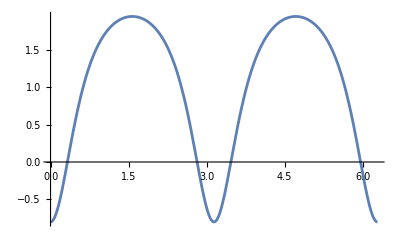

```mathematica
Plot[ω*corr["TrajectoryDeltas"]["Δtθ"]'[qz]-m*corr["TrajectoryDeltas"]["Δϕθ"]'[qz]+k,{qz,0,2Pi}]
```

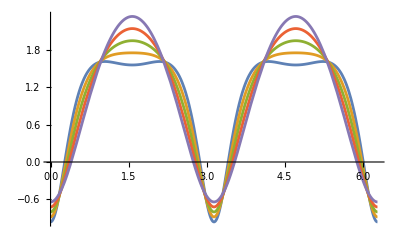

```mathematica
Plot[Table[(ω*corr["TrajectoryDeltas"]["Δtθ"]'[uz-δ*Sin[2*uz]/2]-m*corr["TrajectoryDeltas"]["Δϕθ"]'[uz-δ*Sin[2*uz]/2]+k)*(1-δ*Cos[2*uz]),{δ,-0.2,0.2,0.1}],{uz,0,2Pi},Evaluated->True]
```

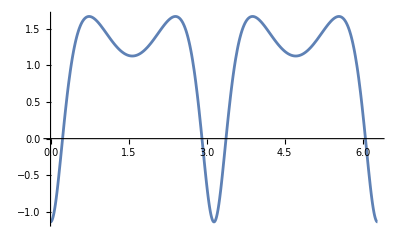

```mathematica
Plot[(ω*corr["TrajectoryDeltas"]["Δtθ"]'[uz-δ*Sin[2*uz]/2]-m*corr["TrajectoryDeltas"]["Δϕθ"]'[uz-δ*Sin[2*uz]/2]+k)*(1-δ*Cos[2*uz])/.{δ->-0.42},{uz,0,2Pi},Evaluated->True]
```

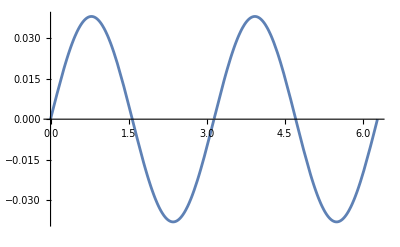

```mathematica
Plot[corr["TrajectoryDeltas"]["Δtθ"][qz],{qz,0,2Pi}]
```

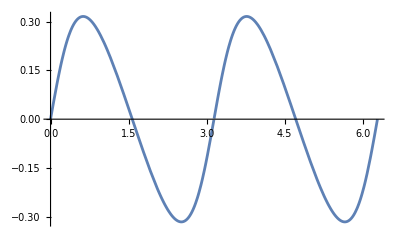

```mathematica
Plot[corr["TrajectoryDeltas"]["Δϕθ"][qz],{qz,0,2Pi}]
```

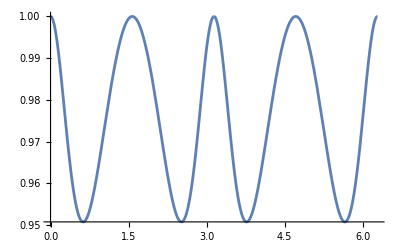

```mathematica
Plot[Cos[Ωϕ*corr["TrajectoryDeltas"]["Δtθ"][qz]-corr["TrajectoryDeltas"]["Δϕθ"][qz]],{qz,0,2Pi}]
```

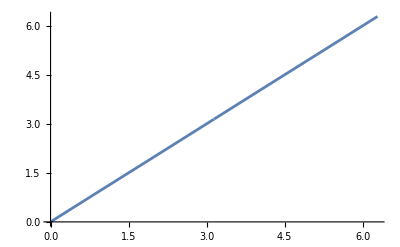

```mathematica
Plot[qz+Ωz*corr["TrajectoryDeltas"]["Δtθ"][qz],{qz,0,2Pi}]
```

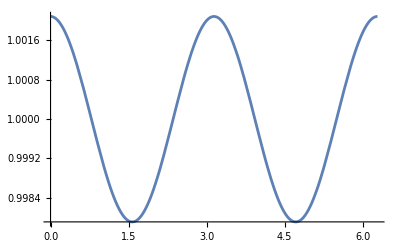

```mathematica
Plot[1+Ωz*corr["TrajectoryDeltas"]["Δtθ"]'[qz],{qz,0,2Pi}]
```

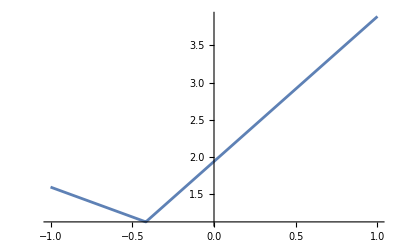

```mathematica
Plot[Max[Abs[(ω*corr["TrajectoryDeltas"]["Δtθ"]'[uz-δ*Sin[2*uz]/2]-m*corr["TrajectoryDeltas"]["Δϕθ"]'[uz-δ*Sin[2*uz]/2]+k)*(1-δ*Cos[2*uz])/.uz->{0,Pi/2}]],{δ,-1,1},Evaluated->True]
```

```mathematica
l=5
m=4
k=3
```

5

4

3

```mathematica
mode=TeukolskySpinModeSphericalCorrection[l,m,k,corr,derivatives,{angparNew,TeukolskySolverHS1spin},WorkingPrecision->32]
```

-1.355294349629068×10^-6

<|l→5,m→4,k→3,n→0,ω→0.19704889267509868165275694221768741554781558,ωCorrection→-0.006676606916700470300720132121251174018854,ωDerivatives→<|r→-0.02714974901659331917281556171720759502971413,x→-0.0128100532590015447815841300481953976710426|>,Amplitudes→<|ℐ→-1.35529434962906784415217614×10^-6-1.08077384327727984412601373×10^-6 ⅈ,ℋ→8.9644066006020411872178645×10^-9+4.4536111175347956637690917×10^-9 ⅈ|>,AmplitudesCorrection→<|ℐ→1.10102451154577590493694194×10^-6+8.43065756651684805276597594×10^-7 ⅈ,ℋ→-1.09142350814259803933453093×10^-8-5.36836755363853670583150515×10^-9 ⅈ|>,AmplitudesDerivatives→<|r→<|ℐ→9.56310316956791042532494122×10^-7+6.20518940846511819338898×10^-7 ⅈ,ℋ→-6.5403721748565637648247847×10^-9-3.0331015517465203126000485×10^-9 ⅈ|>,x→<|ℐ→-6.169165235644922183309793×10^-8-1.1623647329415830190506876×10^-7 ⅈ,ℋ→3.246205029994694158449203×10^-9+1.7141407136892632397261278×10^-9 ⅈ|>|>,α→-0.0009541960451380601028303685278883322641675241,dαdω→-0.011115179308834609040248020808539623231455,S→-0.408584,Fluxes→<|Energy→<|ℐ→6.15845002521009734484931197×10^-12,ℋ→-1.95941681506326298964013814×10^-19|>,AngularMomentum→<|ℐ→1.25013643905411268134645934×10^-10,ℋ→-3.97752413314805087727050625×10^-18|>|>,FluxesCorrection→<|Energy→<|ℐ→-9.43397238276229136018121865×10^-12,ℋ→4.78142493400862898961094569×10^-19|>,AngularMomentum→<|ℐ→-1.8726937294853228701148755×10^-10,ℋ→9.57129767572182965836571373×10^-18|>|>,FluxesDerivatives→<|r→<|Energy→<|ℐ→-6.3644440836857480175991841×10^-12,ℋ→2.9012331856542050633247057×10^-19|>,AngularMomentum→<|ℐ→-1.1197062302420906338823175×10^-10,ℋ→5.3413367517607769006726337×10^-18|>|>,x→<|Energy→<|ℐ→1.6583613803099762120176779×10^-12,ℋ→-1.3991310797185674039311335×10^-19|>,AngularMomentum→<|ℐ→4.1791033920439426603600604×10^-11,ℋ→-3.0987473189144205656036934×10^-18|>|>|>,λ→26.413615826088503924179039847579884211587338,dλdω→-7.941415026021837282002173125174565067451,stepsθ→80|>

```mathematica
1-mode["AmplitudesCorrection"]["ℐ"]/(1.101024512587586*^-6+I*8.43065761154443*^-7)
```

2.57054×10^-9+2.12132×10^-9 ⅈ

```mathematica
1-mode["AmplitudesCorrection"]["ℋ"]/(-1.091423508932585*^-8+I*(-5.368367550991864*^-9))
```

4.8677×10^-10-4.81924×10^-10 ⅈ

```mathematica
a=0.47499999999999997779553950749686919152736663818359375`48.
p=7.67335124506858523574237551656551659107208251953125`48.
e=0
x=0.73749999999999993338661852249060757458209991455078125`48.
```

0.474999999999999977795539507496869191527366638184

7.67335124506858523574237551656551659107208251953

0

0.737499999999999933386618522490607574582099914551

```mathematica
corr=KerrSpinOrbitCorrectionSphericalNew[a,p,e,x,32]
```

FindRoot::precw: The precision of the argument function (0.0005390848401493803010566763820188634058077601686+0.003858561111547031855707183088715374923862631314 («37»)^2+«97» (-«78»+«78» «37») («37»)^5+(-4+«37»)^2 («37»)^6+0.050906640624999990481225342620064778993169512547 (KerrGeodesics`SpecialOrbits`Private`p)^3 (0.32040585937499935201000500484257130807297012+1.047818579101562913621741024439228334283359686 KerrGeodesics`SpecialOrbits`Private`p)) is less than WorkingPrecision (47.).

<|a→0.474999999999999977795539507496869191527366638184,p→7.67335124506858523574237551656551659107208251953,e→0,Inclination→0.737499999999999933386618522490607574582099914551,En0→0.9432358511552541431614144742362072373994179374,Lz0→2.467286376297503233906070767549394296021424568,K0→9.19340698773494305087236252381014708083653492,TrajectoryGeo→{Function[{qt$,qr$,qθ$},qt$+28.6391761272747504079270493595756105429056953 (0.999746963196179537651205074343814547910122604 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.00025313288983336622950397852999156395904101 (π/2+qθ$),0.00101195512430635050872995576876069527251806354],0.00101195512430635050872995576876069527251806354])-0.462599442462710026757343045200533521628305684 (98.611662501186034580132185131626669026910256 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.])+37.6903998028088950629318748775989592021433648 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.]+(0. JacobiCN[0.5 qr$,0.] JacobiSN[0.5 qr$,0.])/(√(1+0. JacobiSN[0.5 qr$,0.]^2)))),Listable],Function[{qr$},(-38.0141834455575184665102938564744896723561408+0. JacobiSN[0.5 qr$,0.]^2)/(-4.95405230797795228792339304451594331764877598+0. JacobiSN[0.5 qr$,0.]^2),Listable],Function[{qθ$},ArcCos[0.67534713296200502805221360244749592715906885771 JacobiSN[1.00025313288983336622950397852999156395904101 (π/2+qθ$),0.00101195512430635050872995576876069527251806354]],Listable],Function[{qϕ$,qr$,qθ$},qϕ$-0.736681383941853698807387693851182729273537895 (1.3563273008070496062115405731286098758392298 (π/2+qθ$)-EllipticPi[0.45609375000000009825473767932634939014881075785,JacobiAmplitude[1.00025313288983336622950397852999156395904101 (π/2+qθ$),0.00101195512430635050872995576876069527251806354],0.00101195512430635050872995576876069527251806354])+0.70362682439468047676439933769186303726000067 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.]),Listable]},MinoFrequenciesGeo→{74.727801052535176260997323195010485012073456,3.3483430378311184023594523245183076064609601,3.4900095586614451721008588042359916604836867},BLFrequenciesGeo→{0.044807193449693034547065342634172519441451138,0.046702960738907557279410811201249212433451854},TrajectoryDeltas→<|Δtr→Function[{qr$},-0.462599442462710026757343045200533521628305684 (98.611662501186034580132185131626669026910256 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.])+37.6903998028088950629318748775989592021433648 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.]+(0. JacobiCN[0.5 qr$,0.] JacobiSN[0.5 qr$,0.])/(√(1+0. JacobiSN[0.5 qr$,0.]^2)))),Listable],Δtθ→Function[{qθ$},28.6391761272747504079270493595756105429056953 (0.999746963196179537651205074343814547910122604 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.00025313288983336622950397852999156395904101 (π/2+qθ$),0.00101195512430635050872995576876069527251806354],0.00101195512430635050872995576876069527251806354]),Listable],Δϕr→Function[{qr$},0.70362682439468047676439933769186303726000067 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.]),Listable],Δϕθ→Function[{qθ$},-0.736681383941853698807387693851182729273537895 (1.3563273008070496062115405731286098758392298 (π/2+qθ$)-EllipticPi[0.45609375000000009825473767932634939014881075785,JacobiAmplitude[1.00025313288983336622950397852999156395904101 (π/2+qθ$),0.00101195512430635050872995576876069527251806354],0.00101195512430635050872995576876069527251806354]),Listable]|>,MinoFrequenciesCorrection→{-0.86823852441334293245415325860772730901447,-0.190516321150631102167406699839609669607311,-0.2640420233451819546545142488522995280304},BLFrequenciesCorrection→{-0.0020288699452052573670894832726408325725048,-0.002990757261415716074949798399891254098186},δEn→-0.004746568431931171274129665575319304492597408,δLz→0.4300219930152017373267107281977399288072329,δK→4.602617821138140104634090957164199468625151,OrbitCorrection→Function[{qz$},Association[δΔt→Δtspinsparsph[qz$,dtgdλcoeff$42582,dtspindλsparcoeff$42582,Υzg$42582,δΥz$42582],δr→δrspinsparsph[qz$,0.474999999999999977795539507496869191527366638184,7.67335124506858523574237551656551659107208251953,0.737499999999999933386618522490607574582099914551,constmot$42582,δconstmot$42582],δz→zspinsparsph[qz$,0.474999999999999977795539507496869191527366638184,7.67335124506858523574237551656551659107208251953,0.737499999999999933386618522490607574582099914551,constmot$42582,δconstmot$42582,ξzcoeff$42582],δΔϕ→Δϕspinsparsph[qz$,dϕgdλcoeff$42582,dϕspindλsparcoeff$42582,Υzg$42582,δΥz$42582],δUr→drdλspinsparsph[qz$,0.474999999999999977795539507496869191527366638184,7.67335124506858523574237551656551659107208251953,0.737499999999999933386618522490607574582099914551,constmot$42582],δUz→dzdλspinsparsph[qz$,0.474999999999999977795539507496869191527366638184,7.67335124506858523574237551656551659107208251953,0.737499999999999933386618522490607574582099914551,constmot$42582,δconstmot$42582,ξzcoeff$42582]]]|>

```mathematica
derivatives=derivativesSph[a,p,x]
```

<|Υz→3.3483430378311184023594523245183076064609601,Υt→74.727801052535176260997323195010485012073456,Υϕ→3.4900095586614451721008588042359916604836867,dΥzdx→-0.2313901794982500782393448390179082325472587,dΥzdr→0.12370302742932820965388768099679679528289213,dΥtdx→-1.05294730436109802190473712330575651222614,dΥtdr→16.649713508635195116752254245820568979239238,dΥϕdx→-0.252641346457514827285164311970954007947286,dΥϕdr→0.1009879089466297570974081185199892500261553,dBLFrequenciesdr→{-0.0083278766117652769000065909684366674176741049,-0.009054234138183094224093655293727700115203357},dMinoFrequenciesdr→{16.649713508635195116752254245820568979239238,0.12370302742932820965388768099679679528289213,0.1009879089466297570974081185199892500261553},dBLFrequenciesdx→{-0.00246508746871737526835298474103553382833553,-0.00272275628315035576855295297991763216522378},dMinoFrequenciesdx→{-1.05294730436109802190473712330575651222614,-0.2313901794982500782393448390179082325472587,-0.252641346457514827285164311970954007947286},dEndr→0.0057285098506425770126820534752728740042136314,dLzdr→0.09151668000937493441179942181474379518540979,dEndx→-0.00461286240671342526798419122721117141344375805,dLzdx→3.17248547782830034514064457426532792926627177,OrbitDerivatives→Function[{qz$},sn$48647=JacobiSN[(Kkz$48647 2 (qz$+π/2))/π,kz$48647];cn$48647=JacobiCN[(2 (qz$+π/2) Kkz$48647)/π,kz$48647];dn$48647=JacobiDN[(2 (qz$+π/2) Kkz$48647)/π,kz$48647];epsilon$48647=JacobiEpsilon[(2 (qz$+π/2) Kkz$48647)/π,kz$48647];cd$48647=JacobiCD[(2 (qz$+π/2) Kkz$48647)/π,kz$48647];sc$48647=JacobiSC[((π+2 qz$) Kkz$48647)/π,kz$48647];dsndkz$48647=-(cn$48647 dn$48647 (2 (qz$+π/2) Ekz$48647-π epsilon$48647+kz$48647 π cd$48647 sn$48647))/(2 (-1+kz$48647) kz$48647 π);dzdr$48647=z1$48647 dsndkz$48647 dkzdr$48647;dzdx$48647=z1$48647 dsndkz$48647 dkzdx$48647-(sn$48647 0.737499999999999933386618522490607574582099914551)/(√(1-0.737499999999999933386618522490607574582099914551^2));dUzdr$48647=(dQdr$48647 cn$48647 dn$48647)/(2 √Q$48647)+1/(2 (-1+kz$48647) kz$48647)√Q$48647 sn$48647 ((kz$48647 cn$48647^2+dn$48647^2) (((π+2 qz$) Ekz$48647)/π-epsilon$48647)+kz$48647 dn$48647 (cn$48647^2 sc$48647+dn$48647 cd$48647 sn$48647)) dkzdr$48647;dUzdx$48647=(dQdx$48647 cn$48647 dn$48647)/(2 √Q$48647)+1/(2 (-1+kz$48647) kz$48647)√Q$48647 sn$48647 ((kz$48647 cn$48647^2+dn$48647^2) (((π+2 qz$) Ekz$48647)/π-epsilon$48647)+kz$48647 dn$48647 (cn$48647^2 sc$48647+dn$48647 cd$48647 sn$48647)) dkzdx$48647;am$48647=JacobiAmplitude[(Kkz$48647 2 (qz$+π/2))/π,kz$48647];damdkz$48647=(dn$48647 (-2 (qz$+π/2) Ekz$48647+π epsilon$48647)-kz$48647 π cn$48647 sn$48647)/(2 (-1+kz$48647) kz$48647 π);dΔtzdr$48647=dttildedr$48647[am$48647]-(dttildedr$48647[π] (qz$+π/2))/π+((En$48647 z2$48647 dn$48647) damdkz$48647 dkzdr$48647)/(-1+En$48647^2);dΔtzdx$48647=dttildedx$48647[am$48647]-(dttildedx$48647[π] (qz$+π/2))/π+((En$48647 z2$48647 dn$48647) damdkz$48647 dkzdx$48647)/(-1+En$48647^2);dΔϕzdr$48647=-(dϕtildedr$48647[am$48647]-(dϕtildedr$48647[π] (qz$+π/2))/π+(Lz$48647 damdkz$48647 dkzdr$48647)/(dn$48647 (-z2$48647+z1$48647^2 z2$48647 sn$48647^2)));dΔϕzdx$48647=-(dϕtildedx$48647[am$48647]-(dϕtildedx$48647[π] (qz$+π/2))/π+(Lz$48647 damdkz$48647 dkzdx$48647)/(dn$48647 (-z2$48647+z1$48647^2 z2$48647 sn$48647^2)));Association[dzdr→dzdr$48647,dzdx→dzdx$48647,dUzdr→dUzdr$48647,dUzdx→dUzdx$48647,dΔtdr→dΔtzdr$48647,dΔtdx→dΔtzdx$48647,dΔϕdr→dΔϕzdr$48647,dΔϕdx→dΔϕzdx$48647]]|>

```mathematica
l=2
m=2
k=1
```

2

2

1

```mathematica
mode=TeukolskySpinModeSphericalCorrection[l,m,k,corr,derivatives,{angparNew,TeukolskySolverHS1spin},WorkingPrecision->32]
```

-0.00001329608758742435

<|l→2,m→2,k→1,n→0,ω→0.13821311492750814910588696503667094430835485,ωCorrection→-0.008010384468036689516989080072423340768876,ωDerivatives→<|r→-0.026436344888131465348193901555892067648080819,x→-0.0079106000350180868054588907008707981587831|>,Amplitudes→<|ℐ→-0.0000132960875874243464662734932-0.00003087893022618957577159162986 ⅈ,ℋ→-7.8635109789127316557430353×10^-7-0.0001797647405117860027597631103 ⅈ|>,AmplitudesCorrection→<|ℐ→2.4983221713177861559207539×10^-6+5.47350826736739495464039118×10^-6 ⅈ,ℋ→-3.308149222006875971138541×10^-6+0.0000955376575463351575049835479 ⅈ|>,AmplitudesDerivatives→<|r→<|ℐ→0.0000109302267495064503981167235+0.0000243514453441945457104686742 ⅈ,ℋ→-0.000013855081006154392584131777+0.000105694271323616103420590213 ⅈ|>,x→<|ℐ→8.8806551094142923134103826×10^-6+0.0000203160820871476671499243482 ⅈ,ℋ→-3.8554894759235872207560033×10^-6+0.000104187461420885966778555186 ⅈ|>|>,α→-0.001885892217321679762671745740722668397,dαdω→-0.01848262268838588150926299757871337466,S→0.153101,Fluxes→<|Energy→<|ℐ→4.70850629057975621930027595×10^-9,ℋ→-2.538784446538891696989029745×10^-10|>,AngularMomentum→<|ℐ→6.81340015099049921338930606×10^-8,ℋ→-3.673724375390088118950598568×10^-9|>|>,FluxesCorrection→<|Energy→<|ℐ→-1.1391268256984332842613241×10^-9,ℋ→2.60309034663299883339790744×10^-10|>,AngularMomentum→<|ℐ→-1.2534802539291631654761531×10^-8,ℋ→3.55386046329795214442119203×10^-9|>|>,FluxesDerivatives→<|r→<|Energy→<|ℐ→-5.67441250769623788526462576×10^-9,ℋ→2.6702040449677024031503466×10^-10|>,AngularMomentum→<|ℐ→-6.9078908017345642561156037×10^-8,ℋ→3.16121205003559088225784142×10^-9|>|>,x→<|Energy→<|ℐ→-5.67143709945413047885850428×10^-9,ℋ→2.8485202735283702586839207×10^-10|>,AngularMomentum→<|ℐ→-7.81683660761473589962430984×10^-8,ℋ→3.91165983645350792650141386×10^-9|>|>|>,λ→3.5634487952219530020241189638577608183,dλdω→-3.15052633045296944724310008817577204,stepsθ→32|>

```mathematica
1-mode["AmplitudesCorrection"]["ℐ"]/(2.498322171321709*^-6+I*5.473508267364412*^-6)
```

-1.803×10^-13-7.99028×10^-13 ⅈ

```mathematica
1-mode["AmplitudesCorrection"]["ℋ"]/(-3.308149222004521*^-6+I*0.0000955376575463298)
```

-5.68434×10^-14-2.26763×10^-14 ⅈ

```mathematica
l=5
m=4
k=3
```

5

4

3

```mathematica
mode=TeukolskySpinModeSphericalCorrection[l,m,k,corr,derivatives,{angparNew,TeukolskySolverHS1spin},WorkingPrecision->32]
```

-3.579693784482547×10^-6

<|l→5,m→4,k→3,n→0,ω→0.32123342330470933275883927270751440805816083,ωCorrection→-0.01804963888127863640106764341748751411026,ωDerivatives→<|r→-0.061200566388028207596394394080220802713835743,x→-0.0182862875387535488792707661427771301459017|>,Amplitudes→<|ℐ→-3.57969378448254692960452835×10^-6-1.85139050426376850906641536×10^-6 ⅈ,ℋ→-5.51137717146255630794902224×10^-8-2.2812483577903112213255749×10^-8 ⅈ|>,AmplitudesCorrection→<|ℐ→3.4422396242991518800239223×10^-6+1.6981461398691015498521294×10^-6 ⅈ,ℋ→7.4792900476626597355077445×10^-8+2.9387177884839656815725416×10^-8 ⅈ|>,AmplitudesDerivatives→<|r→<|ℐ→3.3285843919594740274088681×10^-6+1.44296024064109679455702×10^-6 ⅈ,ℋ→6.6405935869155723668899992×10^-8+2.223050735309943910850547×10^-8 ⅈ|>,x→<|ℐ→0.00001029714424075518089058181+5.2423737503882439987499697×10^-6 ⅈ,ℋ→1.4730212393967053600921011×10^-7+5.9419111824021609797773259×10^-8 ⅈ|>|>,α→-0.0000439603351926034374837504099391220385320968,dαdω→0.00005222982531329501204880720255902752344825,S→-0.408128,Fluxes→<|Energy→<|ℐ→1.2525189257576547753139592×10^-11,ℋ→-1.2061684446977045977978874×10^-19|>,AngularMomentum→<|ℐ→1.5596371172990486882414816×10^-10,ℋ→-1.5019214778950082903845196×10^-18|>|>,FluxesCorrection→<|Energy→<|ℐ→-2.2446354070211605541087338×10^-11,ℋ→3.0879867471462135419109119×10^-19|>,AngularMomentum→<|ℐ→-2.7073872547515450132579555×10^-10,ℋ→3.7607716722817537457047824×10^-18|>|>,FluxesDerivatives→<|r→<|Energy→<|ℐ→-1.7725190096804580491638762×10^-11,ℋ→2.2780043358676385281750675×10^-19|>,AngularMomentum→<|ℐ→-1.9100033944839357318585705×10^-10,ℋ→2.5504297803170897310302012×10^-18|>|>,x→<|Energy→<|ℐ→-7.0394836513184579908662414×10^-11,ℋ→6.2599053593917661170105508×10^-19|>,AngularMomentum→<|ℐ→-8.6767854324437547573811711×10^-10,ℋ→7.7093396766568119348514736×10^-18|>|>|>,λ→26.63249623767770052490977354465666288999342,dλdω→-4.20740993037299625773955420955246820837,stepsθ→80|>

```mathematica
1-mode["AmplitudesCorrection"]["ℐ"]/(3.442239624299351*^-6+I*1.698146139868814*^-6)
```

1.34337×10^-14-9.02056×10^-14 ⅈ

```mathematica
1-mode["AmplitudesCorrection"]["ℋ"]/(7.479290047662328*^-8+I*2.938717788482299*^-8)
```

-1.14353×10^-13-1.77969×10^-13 ⅈ

```mathematica
a=0.9`48
x=0.1`48
σ=0
p=(1-a*x^(3/2))^2/(x*(1-a*x^(3/2))^(1/3)-a*σ*x^3-(a-σ)*(1-a*x^(3/2))^(1/3)*x^(5/2))
xI=1-10^-10
```

0.9

0.1

0

9.8093517635289525576322226247335859891216524384

9999999999/10000000000

```mathematica
corr=KerrSpinOrbitCorrectionSphericalNew[a,p,e,xI,4]
```

<|a→0.9,p→9.8093517635289525576322226247335859891216524384,e→0,Inclination→9999999999/10000000000,En0→0.9513505724954451521643443818153283345998836853,Lz0→3.42876833425989199591804742745552657624049723,K0→6.61802800898350323756776688695104362209354288,TrajectoryGeo→{Function[{qt$,qr$,qθ$},qt$+34.4731806263241623097967375373292517091122623 (0.99999999999967509196846835272848592869235668 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.000000000000324908031531805619357502056812 (π/2+qθ$),1.29963212612627239036942390373089268766717089×10^-12],1.29963212612627239036942390373089268766717089×10^-12])-0.340958356468244237597727489449909357349617703 (390.751960021103053301432116877077688703019 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.])+82.0097439110491233689152924147293481656024331 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.]+(0. JacobiCN[0.5 qr$,0.] JacobiSN[0.5 qr$,0.])/(√(1+0. JacobiSN[0.5 qr$,0.]^2)))),Listable],Function[{qr$},(-82.0097439122599701051941372126379055964248662+0. JacobiSN[0.5 qr$,0.]^2)/(-8.36036324206163903122037652457264445098545456+0. JacobiSN[0.5 qr$,0.]^2),Listable],Function[{qθ$},ArcCos[(√19999999999 JacobiSN[1.000000000000324908031531805619357502056812 (π/2+qθ$),1.29963212612627239036942390373089268766717089×10^-12])/10000000000],Listable],Function[{qϕ$,qr$,qθ$},qϕ$-0.996745624103935237413156080129636011540330807 (1.00000000010032490804158054182509296274906412 (π/2+qθ$)-EllipticPi[19999999999/100000000000000000000,JacobiAmplitude[1.000000000000324908031531805619357502056812 (π/2+qθ$),1.29963212612627239036942390373089268766717089×10^-12],1.29963212612627239036942390373089268766717089×10^-12])-18.4355422687045474284198400586830818710113 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.]),Listable]},MinoFrequenciesGeo→{114.15436125509184950051100397627895416863041,3.4399632678008572452148197378961706115328874,3.609877864099642361202603877817013235971353},BLFrequenciesGeo→{0.030134313135122709627789214077046785574245708,0.03162277660187620682742482123464515253090921},TrajectoryDeltas→<|Δtr→Function[{qr$},-0.340958356468244237597727489449909357349617703 (390.751960021103053301432116877077688703019 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.])+82.0097439110491233689152924147293481656024331 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.]+(0. JacobiCN[0.5 qr$,0.] JacobiSN[0.5 qr$,0.])/(√(1+0. JacobiSN[0.5 qr$,0.]^2)))),Listable],Δtθ→Function[{qθ$},34.4731806263241623097967375373292517091122623 (0.99999999999967509196846835272848592869235668 (π/2+qθ$)-EllipticE[JacobiAmplitude[1.000000000000324908031531805619357502056812 (π/2+qθ$),1.29963212612627239036942390373089268766717089×10^-12],1.29963212612627239036942390373089268766717089×10^-12]),Listable],Δϕr→Function[{qr$},-18.4355422687045474284198400586830818710113 (0.5 qr$-JacobiAmplitude[0.5 qr$,0.]),Listable],Δϕθ→Function[{qθ$},-0.996745624103935237413156080129636011540330807 (1.00000000010032490804158054182509296274906412 (π/2+qθ$)-EllipticPi[19999999999/100000000000000000000,JacobiAmplitude[1.000000000000324908031531805619357502056812 (π/2+qθ$),1.29963212612627239036942390373089268766717089×10^-12],1.29963212612627239036942390373089268766717089×10^-12]),Listable]|>,MinoFrequenciesCorrection→{-0.4963700777959771143111290179305134559281,-0.045723034184265873099984638809059669708135,-0.137723494744947001712341952989145242096012},BLFrequenciesCorrection→{-0.00026950580328952955984134799404444924968706,-0.0010689639302546217932128894424323685557508},δEn→-0.00164392000549390336196612978483082101244593,δLz→0.8156308717496598073775717465480750213186198,δK→4.204119326633802256963206848901343404620828,OrbitCorrection→Function[{qz$},Association[δΔt→Δtspinsparsph[qz$,dtgdλcoeff$59157,dtspindλsparcoeff$59157,Υzg$59157,δΥz$59157],δr→δrspinsparsph[qz$,0.9,9.8093517635289525576322226247335859891216524384,9999999999/10000000000,constmot$59157,δconstmot$59157],δz→zspinsparsph[qz$,0.9,9.8093517635289525576322226247335859891216524384,9999999999/10000000000,constmot$59157,δconstmot$59157,ξzcoeff$59157],δΔϕ→Δϕspinsparsph[qz$,dϕgdλcoeff$59157,dϕspindλsparcoeff$59157,Υzg$59157,δΥz$59157],δUr→drdλspinsparsph[qz$,0.9,9.8093517635289525576322226247335859891216524384,9999999999/10000000000,constmot$59157],δUz→dzdλspinsparsph[qz$,0.9,9.8093517635289525576322226247335859891216524384,9999999999/10000000000,constmot$59157,δconstmot$59157,ξzcoeff$59157]]]|>

```mathematica
derivatives=derivativesSph[a,p,xI];
```

```mathematica
Clear[l,m]
```

```mathematica
l=2
m=2
k=0
```

2

2

0

```mathematica
modes=Table[TeukolskySpinModeSphericalCorrection[l,m,k,corr,derivatives,{angparNew,TeukolskySolverHS1spin},WorkingPrecision->32],{l,2,3},{m,1,l}]
```

-3.741781573224477×10^-6

0.001067222853218579

-3.607958399025378×10^-7

0.00001874002089848086

0.0002507909732025128

{{<|l→2,m→1,k→0,n→0,ω→0.03162277660187620682742482123464515253090921,ωCorrection→-0.0010689639302546217932128894424323685557508,ωDerivatives→<|r→-0.004697982702015851721352061723993769572728786,x→-0.0019241350744181148560971302754408|>,Amplitudes→<|ℐ→-3.7417815732244771863518990572×10^-6-0.000018762283147748864700961093069 ⅈ,ℋ→-0.000084211419412192714951891833609+0.00079328149014417530182881688253 ⅈ|>,AmplitudesCorrection→<|ℐ→-1.8720391541365517318779417531×10^-6-9.8187463425796911602177499491×10^-6 ⅈ,ℋ→0.0000370038424225949401888924042-0.00033931587750297388786258315915 ⅈ|>,AmplitudesDerivatives→<|r→<|ℐ→1.905156625229230091643985776×10^-6+7.6533978986885736397582647617×10^-6 ⅈ,ℋ→0.00003446795909714392718827866798-0.00028914272670083069761046837205 ⅈ|>,x→<|ℐ→-0.00001265225308937091252918541-0.000064219069459596576446783804 ⅈ,ℋ→-0.000142304117602482992435356+0.001357197968104069577772793 ⅈ|>|>,α→-0.000014118456201094682708150653857544616221,dαdω→-0.0011821858363153005724964867589930522532,S→0.313384,Fluxes→<|Energy→<|ℐ→2.91272802216516977517841271×10^-8,ℋ→-7.1498792077136028363437364556×10^-10|>,AngularMomentum→<|ℐ→9.2108547545832995873257286359×10^-7,ℋ→-2.2609903291317544478740956977×10^-8|>|>,FluxesCorrection→<|Energy→<|ℐ→3.240391442339079065994866579×10^-8,ℋ→6.2749849626850777846520069701×10^-10|>,AngularMomentum→<|ℐ→1.0558377587677169381667392741×10^-6,ℋ→1.9078948467407761206718764442×10^-8|>|>,FluxesDerivatives→<|r→<|Energy→<|ℐ→-1.533396620612509141577014302×10^-8,ℋ→5.907437646671148955126376841×10^-10|>,AngularMomentum→<|ℐ→-3.480631291146892059541007593×10^-7,ℋ→1.532195721489891681869332391×10^-8|>|>,x→<|Energy→<|ℐ→2.0284450622900343166012237×10^-7,ℋ→-2.417975646662260792174329×10^-9|>,AngularMomentum→<|ℐ→6.4705513268158052099585256×10^-6,ℋ→-7.783883703837204156665507×10^-8|>|>|>,λ→3.90547343784636802410768091906567096869,dλdω→-2.978419334365942246475773171750734109,stepsθ→32|>,<|l→2,m→2,k→0,n→0,ω→0.06324555320375241365484964246929030506181841,ωCorrection→-0.0021379278605092435864257788848647371115016,ωDerivatives→<|r→-0.009395965404031703442704123447987539145457573,x→-0.0038482701488362297121942605508816|>,Amplitudes→<|ℐ→0.0010672228532185786143809969009-0.00029313657258975008390939107193 ⅈ,ℋ→0.0012520245493264026152151545761+0.00038298598538691996890514993383 ⅈ|>,AmplitudesCorrection→<|ℐ→-0.00010111036486146977419075450047+0.00003278402067091614377368634781 ⅈ,ℋ→-0.00004620309313123912864420465554-0.00002165053609436714767835591945 ⅈ|>,AmplitudesDerivatives→<|r→<|ℐ→-0.00040686617953804138490863496592+0.0001337878648951203790753425062 ⅈ,ℋ→-0.0003799485247305405796131421683-0.0001464405818852703870142652037 ⅈ|>,x→<|ℐ→0.00080295038969114478048023063-0.000211526998343568668197885 ⅈ,ℋ→0.001072338535624739862713877+0.000314490057694850531040325 ⅈ|>|>,α→-0.0020094415578894569271590277929367951422,dαdω→-0.084360268995967773047529346531278946974,S→0.153711,Fluxes→<|Energy→<|ℐ→0.000024368485265091543993967945716,ℋ→-6.8529584065827195115947216484×10^-8|>,AngularMomentum→<|ℐ→0.00077059916565472434125720260419,ℋ→-2.1670957275067767235947219772×10^-6|>|>,FluxesCorrection→<|Energy→<|ℐ→-3.02838683454357681703843412×10^-6,ℋ→6.805776957586714589792959004×10^-9|>,AngularMomentum→<|ℐ→-0.00006971696854866206999532577477,ℋ→1.419619108085126761200232352×10^-7|>|>,FluxesDerivatives→<|r→<|Energy→<|ℐ→-0.00001159685706630056512800382317,ℋ→4.91885320026772830629337523×10^-8|>,AngularMomentum→<|ℐ→-0.0002522420980387144118915495032,ℋ→1.233527158362293719450320442×10^-6|>|>,x→<|Energy→<|ℐ→0.0000395286682384053625475926,ℋ→-1.142426732383512481670109×10^-7|>,AngularMomentum→<|ℐ→0.0012968945022659936340334596,ℋ→-3.744530710508297511966864×10^-6|>|>|>,λ→3.6213730154911307933574246717136974565,dλdω→-5.973406884668742839285673066245861236,stepsθ→32|>},{<|l→3,m→1,k→0,n→0,ω→0.03162277660187620682742482123464515253090921,ωCorrection→-0.0010689639302546217932128894424323685557508,ωDerivatives→<|r→-0.004697982702015851721352061723993769572728786,x→-0.0019241350744181148560971302754408|>,Amplitudes→<|ℐ→-3.6079583990253783725836457806×10^-7-1.5670829187185780696179075237×10^-6 ⅈ,ℋ→0.00010010810327688704365068620493+0.000075007748232467492365970248325 ⅈ|>,AmplitudesCorrection→<|ℐ→1.998126822271409020062659937×10^-8+4.773664855214263700800431623×10^-8 ⅈ,ℋ→-0.000017732746943418893347165220692-0.00001310839264132277477430243133 ⅈ|>,AmplitudesDerivatives→<|r→<|ℐ→1.850729316047537889494803807×10^-7+6.3222582931194130750320984467×10^-7 ⅈ,ℋ→-0.00004421433375948269965652809586-0.00003234532047317793694049756092 ⅈ|>,x→<|ℐ→-1.9449366613196155442254169×10^-6-8.5179403305340806601378889×10^-6 ⅈ,ℋ→0.0005177116625308294284500174+0.000388225243880570891388893 ⅈ|>|>,α→-5.541189839352752477757227723395649205177751×10^-7,dαdω→-0.0000460656312441511627212839272736551128525028,S→-0.298035,Fluxes→<|Energy→<|ℐ→2.057811751345451269077244956×10^-10,ℋ→-6.8999557078540844340316277679×10^-13|>,AngularMomentum→<|ℐ→6.5073721300720933812209656547×10^-9,ℋ→-2.1819575790965503210513144997×10^-11|>|>,FluxesCorrection→<|Energy→<|ℐ→8.58969540174773845237398209×10^-13,ℋ→2.57936102053092675998466451×10^-13|>,AngularMomentum→<|ℐ→2.471356556179937446051558×10^-10,ℋ→7.419075355488356257810138929×10^-12|>|>,FluxesDerivatives→<|r→<|Energy→<|ℐ→-1.071671034349684519719886073×10^-10,ℋ→6.687824154155642650677987852×10^-13|>,AngularMomentum→<|ℐ→-2.422164969782104072129116085×10^-9,ℋ→1.790716966171423831553934793×10^-11|>|>,x→<|Energy→<|ℐ→2.2611760554204515516151643×10^-9,ℋ→-7.112378083612369992428689×10^-12|>,AngularMomentum→<|ℐ→7.1900616033928967480401523×10^-8,ℋ→-2.26240787922342549367729×10^-10|>|>|>,λ→9.924630597812047390362612930415105814888827,dλdω→-2.3667712384005722144993203948000257194993,stepsθ→32|>,<|l→3,m→2,k→0,n→0,ω→0.06324555320375241365484964246929030506181841,ωCorrection→-0.0021379278605092435864257788848647371115016,ωDerivatives→<|r→-0.009395965404031703442704123447987539145457573,x→-0.0038482701488362297121942605508816|>,Amplitudes→<|ℐ→0.000018740020898480863911749623419-7.2311821119052039710325412365×10^-6 ⅈ,ℋ→0.000075117182739805524701247868958-0.000039039614624681996641364981377 ⅈ|>,AmplitudesCorrection→<|ℐ→0.000012762986092589258237006716302-4.753841166319740142919352322×10^-6 ⅈ,ℋ→-0.00004612850032301214700494715822+0.00002398985212595061292345957294 ⅈ|>,AmplitudesDerivatives→<|r→<|ℐ→-8.36381875840173539211226158×10^-6+3.978830781001543666031451788×10^-6 ⅈ,ℋ→-0.00003487374238074826375364882262+0.00001821409015191450310913655372 ⅈ|>,x→<|ℐ→0.000097209958372861025331592949-0.00003720246667821560077934501 ⅈ,ℋ→0.000214537364361044434837344-0.000111469513464801492440178 ⅈ|>|>,α→-0.00007455390221109925850843890418844239425608953,dαdω→-0.0030422694322575800239097698805949307649099,S→-0.372517,Fluxes→<|Energy→<|ℐ→8.026947286296927796910992534×10^-9,ℋ→-1.0629643475946657618750156299×10^-11|>,AngularMomentum→<|ℐ→2.5383436082651521612726660746×10^-7,ℋ→-3.3613884099336146308909968213×10^-10|>|>,FluxesCorrection→<|Energy→<|ℐ→1.142706796045968305183296878×10^-8,ℋ→1.326562281624307266703474504×10^-11|>,AngularMomentum→<|ℐ→3.6993613444267850484860225772×10^-7,ℋ→4.081331213305865579918617789×10^-10|>|>,FluxesDerivatives→<|r→<|Energy→<|ℐ→-4.996181076937378033868829144×10^-9,ℋ→1.079738437586412580119801217×10^-11|>,AngularMomentum→<|ℐ→-1.202826585560321818420619779×10^-7,ℋ→2.915053928203993435316553106×10^-10|>|>,x→<|Energy→<|ℐ→8.416450431266576590512265×10^-8,ℋ→-6.03382646519490851110466×10^-11|>,AngularMomentum→<|ℐ→2.676960248468568578636315×10^-6,ℋ→-1.928516333450629696914296×10^-9|>|>|>,λ→9.6983415558157109716111209036959327774330205,dλdω→-4.739275724235213484023180868362180912005,stepsθ→32|>,<|l→3,m→3,k→0,n→0,ω→0.09486832980562862048227446370393545759272762,ωCorrection→-0.0032068917907638653796386683272971056672524,ωDerivatives→<|r→-0.01409394810604755516405618517198130871818636,x→-0.0057724052232543445682913908263224|>,Amplitudes→<|ℐ→0.00025079097320251277755367572529+0.00050420064852031434175832969016 ⅈ,ℋ→-0.00003220702786743697245896164306-0.00022815792417724958397165086268 ⅈ|>,AmplitudesCorrection→<|ℐ→-0.0000353065335924793496246892665-0.00006000011764769860920649783921 ⅈ,ℋ→5.2541539466219338286682333×10^-7+7.903755051562890341359562417×10^-6 ⅈ|>,AmplitudesDerivatives→<|r→<|ℐ→-0.0001271727153814355827843101451-0.0002074101736100717567140754259 ⅈ,ℋ→0.0000106392678158736618065110485+0.00009309535926972888831492329181 ⅈ|>,x→<|ℐ→0.000290760799723347924665044+0.0006043245595178243894976649 ⅈ,ℋ→-0.0000445557085588882802940022-0.0003081102740595481201248588 ⅈ|>|>,α→-0.0017709095740107806554268532237601538836,dαdω→-0.049364580762477806540388721764693885157,S→-0.223605,Fluxes→<|Energy→<|ℐ→2.8039069596148409184262717732×10^-6,ℋ→-8.3135016186462515999777954719×10^-10|>,AngularMomentum→<|ℐ→0.000088667323395267026643782671397,ℋ→-2.6289600446258739725917624596×10^-8|>|>,FluxesCorrection→<|Energy→<|ℐ→-5.019932092403715192229777937×10^-7,ℋ→7.511481610081353360309112208×10^-11|>,AngularMomentum→<|ℐ→-0.00001287714370769229407888339019,ℋ→1.48665571258432311672370657×10^-9|>|>,FluxesDerivatives→<|r→<|Energy→<|ℐ→-1.580206350664141117264440427×10^-6,ℋ→7.555069967349124580941431949×10^-10|>,AngularMomentum→<|ℐ→-0.00003679780601713800466319181193,ℋ→1.998556029890125581641752025×10^-8|>|>,x→<|Energy→<|ℐ→7.0190215637887823026235474×10^-6,ℋ→-2.213823684906852984206172×10^-9|>,AngularMomentum→<|ℐ→0.00022735604659907765697149335,ℋ→-7.160688182844729166894696×10^-8|>|>|>,λ→9.32056172917798683917351636888776735934,dλdω→-7.124148133681972601006675180914799205,stepsθ→32|>}}

```mathematica
Sum[modes[[il,im]]["FluxesCorrection"]["Energy"]["ℋ"],{il,1,2},{im,1,Length[modes[[il]]]}]
```

7.521913828874332067204284035×10^-9

```mathematica
Sum[modes[[il,im]]["FluxesDerivatives"]["r"]["Energy"]["ℋ"],{il,1,2},{im,1,Length[modes[[il]]]}]
```

5.054624893087059010660679899×10^-8

```mathematica
%100+%101/(-(1-a*x^(3/2))^2/(-a*x^3+(1-a*x^(3/2))^(1/3)*x^(5/2))/p^2)
```

-3.97921768651893806429151332×10^-9

```mathematica
2*mode["Fluxes"]["Energy"]["ℐ"]
```

6.39967596423681149336498×10^-25

```mathematica
1-%/(6.3996759655167373927304246418119591170872359389738318`30.10099681944018*^-25)
```

1.9999854777993×10^-10

```mathematica
2*mode["FluxesCorrection"]["Energy"]["ℐ"]
```

-1.2765247906990777453×10^-31

```mathematica
2*mode["FluxesDerivatives"]["r"]["Energy"]["ℐ"]
```

-3.1998056515205634740284×10^-29

```mathematica
%80+%79/(-(1-a*x^(3/2))^2/(-a*x^3+(1-a*x^(3/2))^(1/3)*x^(5/2))/p^2)
```

-2.6753721337226955197×10^-32

```mathematica
1-%/(-2.6753721342407005*^-32)
```

1.9362×10^-10

```mathematica
2*mode["FluxesCorrection"]["Energy"]["ℋ"]
```

2.705182007090107823164×10^-44

```mathematica
2*mode["FluxesDerivatives"]["r"]["Energy"]["ℋ"]
```

1.1714731125673825834193×10^-41

```mathematica
%86+%87/(-(1-a*x^(3/2))^2/(-a*x^3+(1-a*x^(3/2))^(1/3)*x^(5/2))/p^2)
```

-9.88798023200686565364×10^-45

```mathematica
1-%/(-9.88798023404135*^-45)
```

2.05753×10^-10